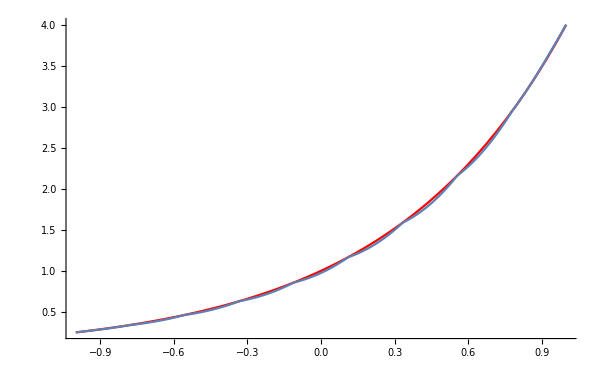

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
func[x] = 4^x;
plotf = Plot[func[x],{x,-1,1},PlotStyle->Red];
list1 = ReadList["uniform.txt", Number, RecordLists->True];
list2 = ReadList["chebysh.txt", Number, RecordLists->True];
list3= ReadList["spline.txt", Number, RecordLists->True];
n=list3[[1,1]];
listplot={};
For[i=1,i<n,i++,
spline=list3[[i+1,1]]+list3[[i+1,2]]*(x-list1[[1,i]])+list3[[i+1,3]]*(x-list1[[1,i]])^2+list3[[i+1,4]]*(x-list1[[1,i]])^3;
plot=Plot[spline==0,{x,list1[[1,i]],list1[[1,i+1]]}];
listplot=Append[listplot,plot];
]
Show[plotf,listplot,PlotRange->All,ImageSize->600]
```

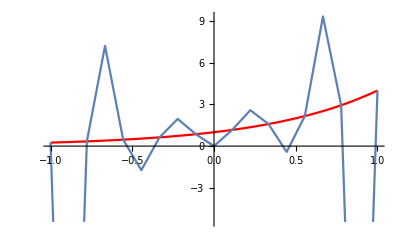

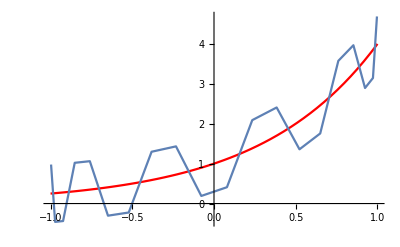

```mathematica
unipoints = ReadList["uni_points.txt", Number, RecordLists->True];
plotu = ListLinePlot[Partition[Riffle[unipoints[[1]], unipoints[[2]]],2]];
Show[plotf, plotu, PlotRange->All]
chebpoints = ReadList["cheb_points.txt", Number, RecordLists->True];
plotc= ListLinePlot[Partition[Riffle[chebpoints[[1]], chebpoints[[2]]],2]];
Show[plotf, plotc, PlotRange->All]
```